```mathematica
data = ReadList["./GitHub/PHYS-3181/homework1/output.log",{Real,Real,Real}]
```

{{0.,0.,0.},{0.062832,0.062791,-0.062791},{0.125664,0.125333,-0.125333},{0.188496,0.187381,-0.187381},{0.251327,0.24869,-0.24869},{0.314159,0.309017,-0.309017},{0.376991,0.368125,-0.368125},{0.439823,0.425779,-0.425779},{0.502655,0.481754,-0.481754},{0.565487,0.535827,-0.535827},{0.628319,0.587785,-0.587785},{0.69115,0.637424,-0.637424},{0.753982,0.684547,-0.684547},{0.816814,0.728969,-0.728969},{0.879646,0.770513,-0.770513},{0.942478,0.809017,-0.809017},{1.00531,0.844328,-0.844328},{1.06814,0.876307,-0.876307},{1.13097,0.904827,-0.904827},{1.19381,0.929776,-0.929776},{1.25664,0.951057,-0.951057},{1.31947,0.968583,-0.968583},{1.3823,0.982287,-0.982287},{1.44513,0.992115,-0.992115},{1.50796,0.998027,-0.998027},{1.5708,1.,-1.},{1.63363,0.998027,-0.998027},{1.69646,0.992115,-0.992115},{1.75929,0.982287,-0.982287},{1.82212,0.968583,-0.968583},{1.88496,0.951057,-0.951057},{1.94779,0.929776,-0.929776},{2.01062,0.904827,-0.904827},{2.07345,0.876307,-0.876307},{2.13628,0.844328,-0.844328},{2.19912,0.809017,-0.809017},{2.26195,0.770513,-0.770513},{2.32478,0.728969,-0.728969},{2.38761,0.684547,-0.684547},{2.45044,0.637424,-0.637424},{2.51327,0.587785,-0.587785},{2.57611,0.535827,-0.535827},{2.63894,0.481754,-0.481754},{2.70177,0.425779,-0.425779},{2.7646,0.368125,-0.368125},{2.82743,0.309017,-0.309017},{2.89027,0.24869,-0.24869},{2.9531,0.187381,-0.187381},{3.01593,0.125333,-0.125333},{3.07876,0.062791,-0.062791},{3.14159,0.,0.},{3.20443,-0.062791,0.062791},{3.26726,-0.125333,0.125333},{3.33009,-0.187381,0.187381},{3.39292,-0.24869,0.24869},{3.45575,-0.309017,0.309017},{3.51858,-0.368125,0.368125},{3.58142,-0.425779,0.425779},{3.64425,-0.481754,0.481754},{3.70708,-0.535827,0.535827},{3.76991,-0.587785,0.587785},{3.83274,-0.637424,0.637424},{3.89558,-0.684547,0.684547},{3.95841,-0.728969,0.728969},{4.02124,-0.770513,0.770513},{4.08407,-0.809017,0.809017},{4.1469,-0.844328,0.844328},{4.20973,-0.876307,0.876307},{4.27257,-0.904827,0.904827},{4.3354,-0.929776,0.929776},{4.39823,-0.951057,0.951057},{4.46106,-0.968583,0.968583},{4.52389,-0.982287,0.982287},{4.58673,-0.992115,0.992115},{4.64956,-0.998027,0.998027},{4.71239,-1.,1.},{4.77522,-0.998027,0.998027},{4.83805,-0.992115,0.992115},{4.90089,-0.982287,0.982287},{4.96372,-0.968583,0.968583},{5.02655,-0.951057,0.951057},{5.08938,-0.929776,0.929776},{5.15221,-0.904827,0.904827},{5.21504,-0.876307,0.876307},{5.27788,-0.844328,0.844328},{5.34071,-0.809017,0.809017},{5.40354,-0.770513,0.770513},{5.46637,-0.728969,0.728969},{5.5292,-0.684547,0.684547},{5.59204,-0.637424,0.637424},{5.65487,-0.587785,0.587785},{5.7177,-0.535827,0.535827},{5.78053,-0.481754,0.481754},{5.84336,-0.425779,0.425779},{5.90619,-0.368125,0.368125},{5.96903,-0.309017,0.309017},{6.03186,-0.24869,0.24869},{6.09469,-0.187381,0.187381},{6.15752,-0.125333,0.125333},{6.22035,-0.062791,0.062791},{6.28319,0.,0.}}

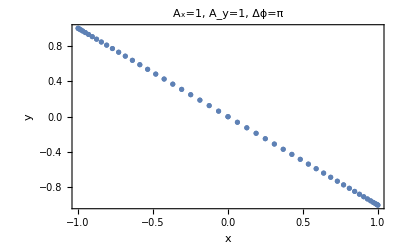

```mathematica
g = ListPlot[Transpose[{data[[All,2]],data[[All,3]]}],Frame->True,FrameLabel->{"x","y"},PlotLabel->"A_x=1, A_y=1, Δϕ=π"]
```

```mathematica
Export["C:\\Users\\Caden Gobat\\Documents\\GitHub\\PHYS-3181\\homework1\\plot_1,1,pi.pdf",g]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework1\plot_1,1,pi.pdf

```mathematica
Directory[]
```

C:\Users\Caden Gobat\Documents